```mathematica
En[r_]:=1/(2μ*r^2)-A/r+k*r
En'[r]
Solve[En'[r]==0,r]
```

0.2-4.44444/r^3+4/(3 r^2)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-1.02345-3.13194 ⅈ},{r→-1.02345+3.13194 ⅈ},{r→2.04691}}

{0.288377,{r→2.04691}}

0.530385

-0.65139

0.409381

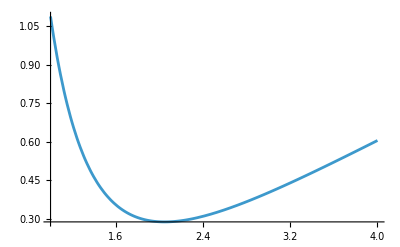

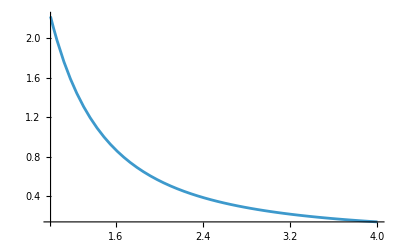

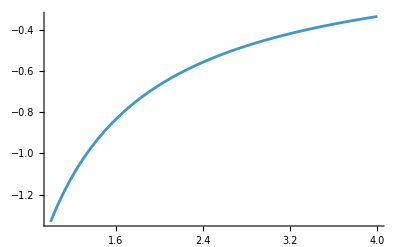

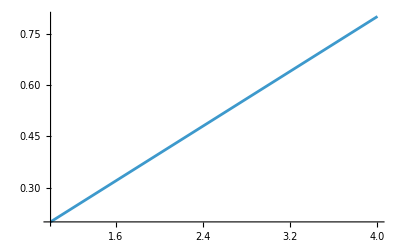

```mathematica
mQ=0.45;
α=1;
μ=mQ/2;
A=4α/3;
k=0.2;
En[r_]:=1/(2μ*r^2)-A/r+k*r
E1[r_]:=1/(2μ*r^2)
E2[r_]:=-A/r
E3[r_]:=k*r
Minimize[{En[r],r>0.5},r]
E1[2.0469063118107327]
E2[2.0469063118107327]
E3[2.0469063118107327]
Plot[En[r],{r,1,4}]
Plot[E1[r],{r,1,4}]
Plot[E2[r],{r,1,4}]
Plot[E3[r],{r,1,4}]
```

{0.239034,{r→1.42192}}

0.329732

-0.375081

0.284383

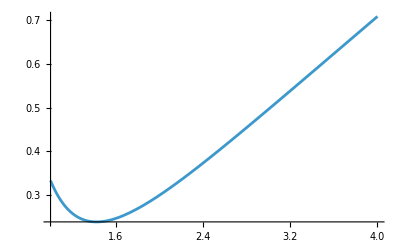

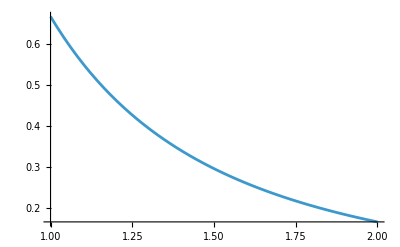

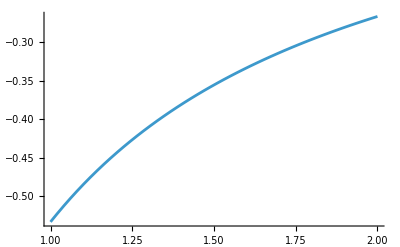

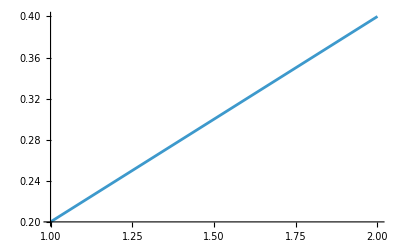

```mathematica
mQ=1.5;
α=0.4;
μ=mQ/2;
A=4α/3;
k=0.2;
En[r_]:=1/(2μ*r^2)-A/r+k*r
E1[r_]:=1/(2μ*r^2)
E2[r_]:=-A/r
E3[r_]:=k*r
Minimize[{En[r],r>0.5},r]
E1[1.4219156275419749]
E2[1.4219156275419749]
E3[1.4219156275419749]
Plot[En[r],{r,1,4}]
Plot[E1[r],{r,1,2}]
Plot[E2[r],{r,1,2}]
Plot[E3[r],{r,1,2}]
```

{-0.197924,{r→0.668979}}

0.465515

-0.797235

0.133796

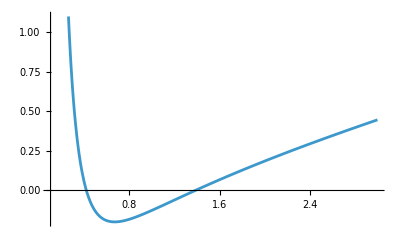

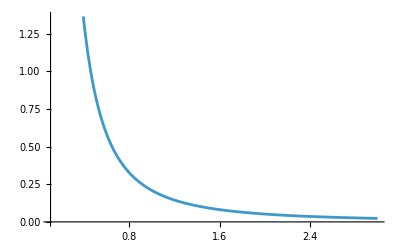

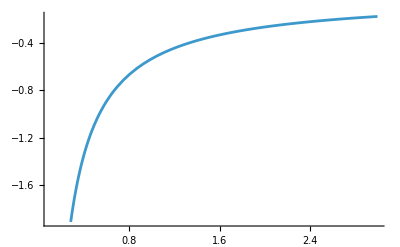

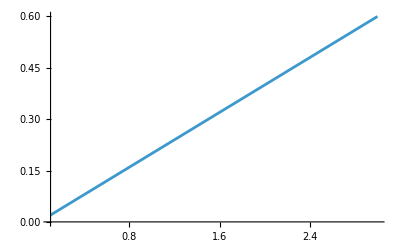

```mathematica
mQ=4.8;
α=0.4;
μ=mQ/2;
A=4α/3;
k=0.2;
En[r_]:=1/(2μ*r^2)-A/r+k*r
E1[r_]:=1/(2μ*r^2)
E2[r_]:=-A/r
E3[r_]:=k*r
Minimize[{En[r],r>0.1},r]
E1[0.6689788054145663]
E2[0.6689788054145663]
E3[0.6689788054145663]
Plot[En[r],{r,0.1,3}]
Plot[E1[r],{r,0.1,3}]
Plot[E2[r],{r,0.1,3}]
Plot[E3[r],{r,0.1,3}]
```

```mathematica
1.166*10^(-5)*14.19^3
1.166*10^(-5)*173^3
```

0.0333155

60.3722

```mathematica
6.582*10^(-22)/33.3
6.582*10^(-22)/60400
```

1.97658×10^-23

1.08974×10^-26

0.514352+0.86652 x

0.408485+0.81079 x

0.183671

0.196296

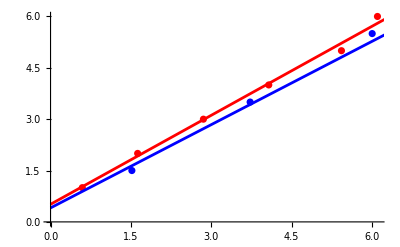

```mathematica
mesondata={{0.77^2,1},{1.275^2,2},{1.689^2,3},{2.018^2,4},{2.33^2,5},{2.47^2,6}};
baryondata={{1.232^2,3/2},{1.93^2,7/2},{2.45^2,11/2},{2.99^2,15/2}};
linemeson=Fit[mesondata,{1,x},x]
linebaryon=Fit[baryondata,{1,x},x]
kmeson=(1/linemeson[[2]][[1]])/(2Pi)
kbaryon=(1/linebaryon[[2]][[1]])/(2Pi)
Show[ListPlot[mesondata,PlotStyle->Red],ListPlot[baryondata,PlotStyle->Blue],Plot[linemeson,{x,0,9},PlotStyle->Red],Plot[linebaryon,{x,0,9},PlotStyle->Blue]]
```

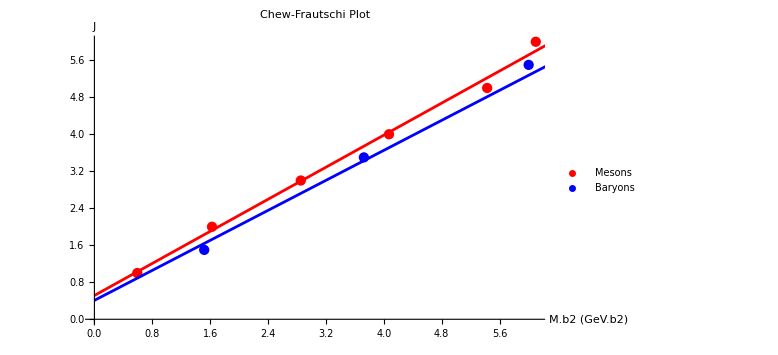

```mathematica
Show[(*1. Meson 資料點 (加入圖例標籤 "Mesons")*)ListPlot[mesondata,PlotStyle->Red,PlotLegends->{"Mesons"}],(*2. Baryon 資料點 (加入圖例標籤 "Baryons")*)ListPlot[baryondata,PlotStyle->Blue,PlotLegends->{"Baryons"}],(*3. Meson 擬合線 (不需要標籤，因為它和資料點同色)*)Plot[linemeson,{x,0,9},PlotStyle->Red],(*4. Baryon 擬合線 (不需要標籤，因為它和資料點同色)*)Plot[linebaryon,{x,0,9},PlotStyle->Blue],(*---在這裡加入全域標籤---*)(*加入主標題*)PlotLabel->"Chew-Frautschi Plot",(*加入 X 和 Y 座標軸標籤*)(*格式:AxesLabel->{"X 軸標籤","Y 軸標籤"}*)AxesLabel->{"M.b2 (GeV.b2)","J"},(*(可選) 讓字體大一點，更已閱讀*)BaseStyle->{FontSize->12},ImageSize->Large]
```